```mathematica
(* Applied Field direction *)
uh={1,0,0};
uk={0,0,1};
(* Shape anisotropy (demag field) *)
Ndemag={{0,0,0},{0,0,0},{0,0,1}};
p={1/Sqrt[2],0,1/Sqrt[2]}; (* vecteur polarization *)
ku2=0;
```

```mathematica
(* Uniaxial anisotropy in J/m3 *)
ku1=1026480; 
(* Saturation magnetization in A/m *)
Ms= 11.72*10^5;
```

```mathematica
(* Spin transfer torque direction *)

bV [V_]:= 0.03*V^2
b = 0.03;
(* Gilbert damping *)
α=0.01;

(* Constant definitions *)
μ =4*Pi*10^-7;(* free space permeability *)
γ=(2*Pi)*28*10^9;(* gyromagnetic factor rad/sT *)
```

```mathematica
Needs["FourierSeries`"]
Needs["VariationalMethods`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
(* magnetization function definition *)
m[θ_,ϕ_]:={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};  (* aimantation normalisée en coordonnées polaires *)
M[θ_,ϕ_]:=Ms*m[θ,ϕ]; (* aimantation en coordonnées polaires *)

(* definition des énergies ne dépendant pas de H *)
Edem[θ_,ϕ_]:= μ /2*Ms^2*m[θ,ϕ].(Ndemag.m[θ,ϕ]);
Eani[θ_,ϕ_]:=-ku1(uk.m[θ,ϕ])^2-ku2(uk.m[θ,ϕ])^4;

(* definition des énergies dépendant de H et de V*)
Ezeeman[θ_,ϕ_,H_]:= - μ Ms(H/μ)m[θ,ϕ].uh; 

Estt[θ_,ϕ_,V_]:= - μ Ms(bV[V]/μ)m[θ,ϕ].p; 
Etot[θ_,ϕ_,H_,V_]:=Ezeeman[θ,ϕ,H]+Estt[θ,ϕ,V]+Eani[θ,ϕ]+Edem[θ,ϕ];
(* definition du Lagrangien *)
ℒ[t_,H_,V_]:=-Ms/γ*D[ϕ[t],t]*Cos[θ[t]]-Etot[θ[t],ϕ[t],H,V];

(* Damping fonction de Rayleigh *)
ℱdamping[D[θ[t],t],D[ϕ[t],t]]=α*Ms/(2γ)*(Dt[m[θ[t],ϕ[t]],t].Dt[m[θ[t],ϕ[t]],t])//FullSimplify;
```

```mathematica
Condition initiales
```

```mathematica
(* Max time calculation *)
tmax=10 10^-9;(* in s*)

Print[x];
V= -0.0;(* Initial position *)
H =0.2;(*T*)
(*V=0.1;*)(*V*)
{θi,ϕi}={1,Pi/2}; 
(* direction initiale de l'aimantation dans la base canonique *)

(* Spin transfer torque *)
aV=0.008*V; (* Slonc Torque for MTJ avec aV/V en  *)
(*Print[aV];*)
(* Rayleigh's dissipaµtion functions : régférence http://www.academia.edu/4733940/Spin_transfer_and_current-induced_switching_in_antiferromagnets, soit *)
ℱslonc[D[θ[t],t],D[ϕ[t],t]]=Ms*aV*p.(m[θ[t],ϕ[t]]×Dt[m[θ[t],ϕ[t]],t])//FullSimplify;
(* reférence bibliographique : Lagrangian formulation of the linear autonomous magnetization
dynamics in spin-torque auto-oscillators, G.Consolo,G.Gubbiotti,L.Giovannini,R.Zivieri, Applied Mathematics and Computation 217 (2011) 8204–8215 *)

dℱθ=D[(ℱdamping[D[θ[t],t],D[ϕ[t],t]]+ℱslonc[D[θ[t],t],D[ϕ[t],t]]),D[θ[t],t]];
dℱϕ=D[(ℱdamping[D[θ[t],t],D[ϕ[t],t]]+ℱslonc[D[θ[t],t],D[ϕ[t],t]]),D[ϕ[t],t]];

(* full numericall LLG and time evolution evaluation *)
LLGwithoutdamping=EulerEquations[ℒ[t,H,V],{θ[t],ϕ[t]},t];
System={LLGwithoutdamping[[1]]//.0-> dℱθ,LLGwithoutdamping[[2]]//.0-> dℱϕ};
Evol=NDSolve [Flatten[{System,θ[0]==θi,ϕ[0]==ϕi}],{θ,ϕ},{t,0,tmax},Method->Automatic, StartingStepSize->1*10^-15];
θcalc[t_]:=Evaluate[θ[t]/.Evol][[1]];
ϕcalc[t_]:=Evaluate[ϕ[t]/.Evol][[1]];
Show[{ParametricPlot3D[{{m[θcalc[t],ϕcalc[t]]}},{t,0,tmax},PlotStyle->{Black,Thin},Axes->False,Boxed->False],
ParametricPlot3D[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]},{u,0,2π},{v,0,π},PlotStyle-> None,PerformanceGoal->"Quality",Mesh->12,MeshStyle->Directive[{Gray,Thin,Dotted}],Boxed->False,Axes->None],Graphics3D[{RGBColor[0.7450980392156863, 0.06666666666666667, 0.00392156862745098], Sphere[m[θcalc[tmax],ϕcalc[tmax]],0.03],RGBColor[0.6313725490196078, 0.6313725490196078, 0.24705882352941178], Sphere[m[θcalc[0],ϕcalc[0]],0.03],Black,Thin,Dashed,Arrow[{{0,0,-1},{0,0,1.2}}],Arrow[{{0,-1,0},{0,1.2,0}}],Arrow[{{-1,0,0},{1.2,0,0}}]}]},PlotRange->All]


(*
Print[Show[{ParametricPlot3D[{{m[θcalc[t],ϕcalc[t]]},{m[θi,2Pi *t/tmax]}},{t,0,tmax},PlotStyle->{Red,Blue},AxesLabel->{mx,my,mz}],Graphics3D[{Opacity[0.3],Gray,Sphere[{0,0,0}],Black,Thick,Line[{{0,0,0},m[θcalc[tmax],ϕcalc[tmax]]}]}]},PlotRange->All]];*)(*


Print[Plot[θcalc[t],{t,0,tmax},PlotRange->All]];
Print[Plot[ϕcalc[t],{t,0,tmax}]];*)
```

x

-Graphics3D-

```mathematica
Show[%540,ViewPoint->Above]
```

-Graphics3D-

```mathematica
SetDirectory["C:\\Users\\Marion\\Documents\\RedactionThese\\Energy"];
```

```mathematica
Export["TrajTiltAniHm150mTVm750mV.png",%]
```

General::noinfo: Input expression                                  -8
InterpolatingFunction[{{0., 4. 10  }}, <>] contains insufficient information to interpret the result.

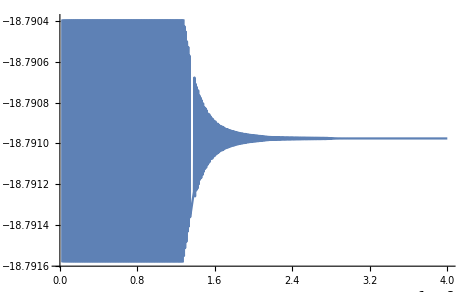

```mathematica
Plot[%333,{t,0.,4.*^-8}]
```

```mathematica
D[ϕcalc[t],t]
```

-8
InterpolatingFunction[{{0., 4. 10  }}, <>][t]

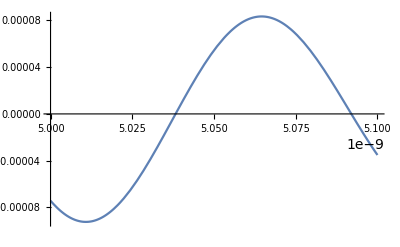

```mathematica
Plot[ϕcalc[t],{t,0.5×10^-8,0.51×10^-8}]
```

```mathematica
dataF=   Table[{t,θcalc[t]},  {t,4.*^-9,1*^-8,1.*^-12}]
```

{{4.×10^-9,1.45866},{4.001×10^-9,1.45881},{4.002×10^-9,1.4589},{4.003×10^-9,1.45895},{4.004×10^-9,1.45894},{4.005×10^-9,1.45887},{4.006×10^-9,1.45875},{4.007×10^-9,1.45858},5986,{9.994×10^-9,0.836047},{9.995×10^-9,0.83468},{9.996×10^-9,0.833275},{9.997×10^-9,0.831835},{9.998×10^-9,0.83036},{9.999×10^-9,0.828852},{1.×10^-8,0.827312}}
 |  |  |  |

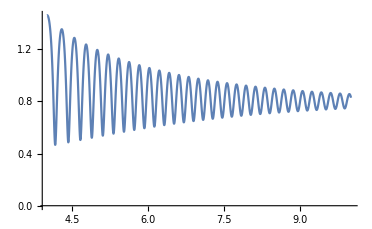

```mathematica
ListPlot[dataF,Joined->True]
```

```mathematica
ArrayPlot[dataF]
```

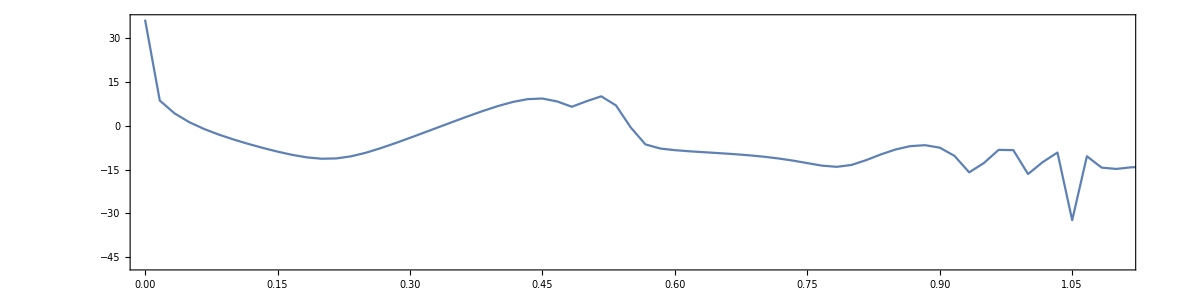

```mathematica
Periodogram[dataF[[All,2]],SampleRate->1.*^12,Frame->True,GridLinesStyle->Directive[Red,Dashed],AspectRatio->1/4,PlotRange->{{5*^7,1.1*^10},All}]
```